```mathematica
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Miscellaneous`;
```

```mathematica
<<PhysicalApplications`Astrophysics`Cosmology`Kinematics`;
```

Cosmology:Kinematics: Warnings : Assumptions inherent in code only apply at relatively low redshifts z<10^9, so T<<m_e

```mathematica
ΩM=0.3;
ΩΛ=0.7;
α=-1;
c=3*10^8;
M0=(1.989*10^30 *6.674*10^-11)/c^2;(*Unitless *)
```

```mathematica
En[z_]:=√(ΩM(1+z)^3+ΩΛ)

Pok[z_,Mc_]:=If[PracticalDistanceLuminosity[z]/(Dres(Mc/(1.2 M0))^(5/6) Mega Parsec)<1,DetectorCumulativeAngleFactorGreater["MonteCarlo"][PracticalDistanceLuminosity[z]/(Dres(Mc/(1.2 M0))^(5/6) Mega Parsec)],0]

Rv[z_]:=0.015 (1+z)^2.7/(1+((1+z)/2.9)^5.6)
```

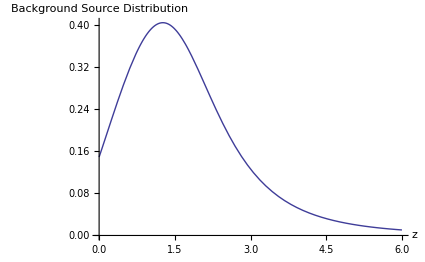

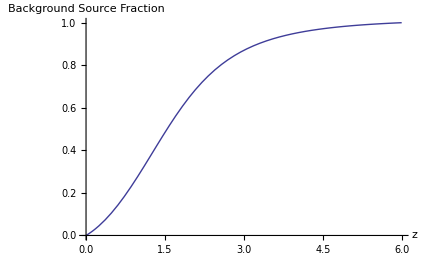

```mathematica
PDF0[z0_]:=Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1

Plot[PDF0[z],{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425]

Clear[P]
Clear[sol0]
sol0= P/.NDSolve[{P'[z]==PDF0[z], P[0]==0}, P,{z,0,6}][[1]];

Plot[sol0[z],{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Fraction",Black,20,Bold]},TicksStyle->15,ImageSize->425]
```

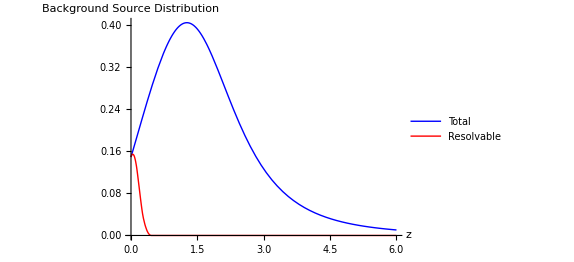

```mathematica
Dres = 440 (*# of Mega Parsecs*);

Mc = 10 M0;

B0=NIntegrate[Rv[z]/((1+z)^(1/3)En[z]),{z,0,6}];

PDF0[z0_]:=Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1
PDFp[z0_]:=(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1

Plot[{PDF0[z],PDFp[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.60}]]
```

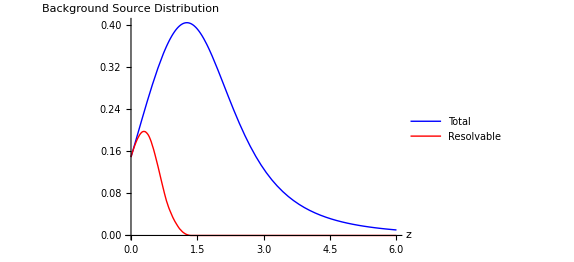

```mathematica
Dres = 440 (*# of Mega Parsecs*);

Mc = 50 M0;

B0=NIntegrate[Rv[z]/((1+z)^(1/3)En[z]),{z,0,6}];

PDF0[z0_]:=Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1
PDFp[z0_]:=(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1

Plot[{PDF0[z],PDFp[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.60}]]
```

Power::infy: Infinite expression 1/0.^1.2 encountered.

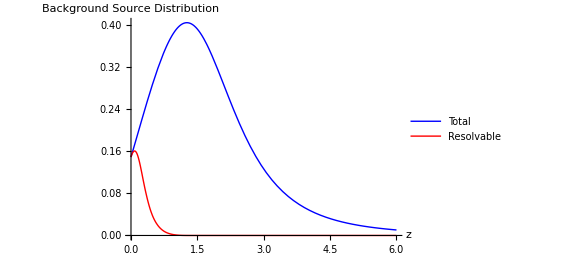

InterpolatingFunction::dmval: Input value {1.00257} lies outside the range of data in the interpolating function. Extrapolation will be used.

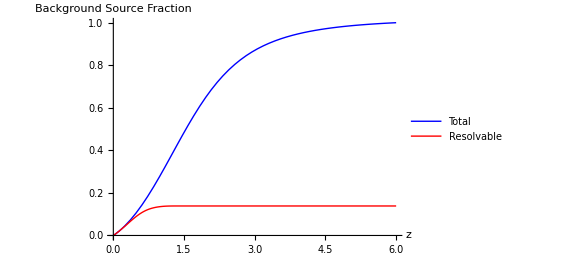

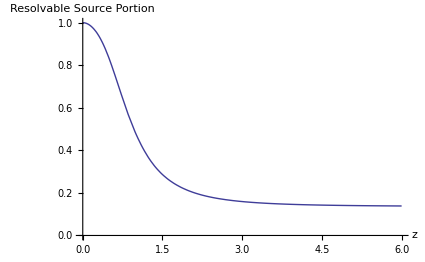

0.861353

```mathematica
Dres = 440 (*# of Mega Parsecs*);

PDF0m[z0_]:=NIntegrate[Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]
PDFpm[z0_]:=NIntegrate[(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]

Plot[{PDF0m[z],PDFpm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Clear[P]
Clear[sol0m]
sol0m= P/.NDSolve[{P'[z]==PDF0[z], P[0]==0}, P,{z,0,6}][[1]];
Clear[P]
Clear[solzm]
solzm= P/.NDSolve[{P'[z]==PDFp[z], P[0]==0}, P,{z,0,6}][[1]];

Plot[{sol0m[z],solzm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Fraction",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1},PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Plot[{solzm[z]/sol0m[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Resolvable \n Source \n Portion",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1}]

1-solzm[6]/sol0m[6](*lambda*)
```

Power::infy: Infinite expression 1/0.^1.2 encountered.

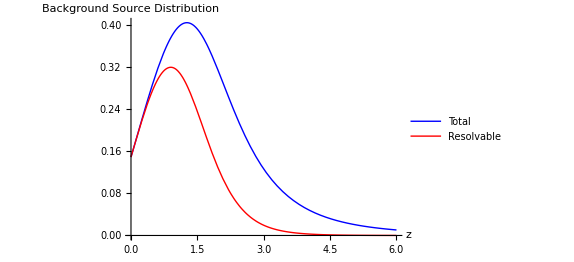

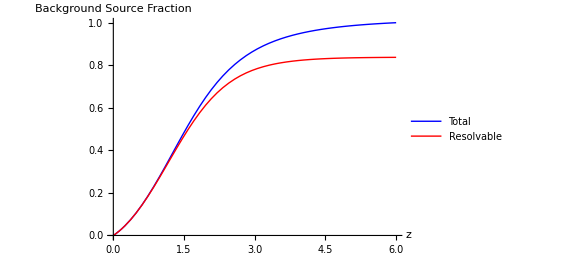

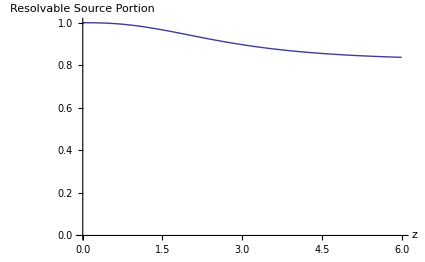

0.162813

```mathematica
Dres = 4440 (*# of Mega Parsecs*);

PDF0m[z0_]:=NIntegrate[Rv[z0]/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]
PDFpm[z0_]:=NIntegrate[(Rv[z0]Pok[z0,Mc])/((1+z0)^(1/3)En[z0])(B0)^-1(1/Mc^2),{Mc,10 M0,50 M0}]/NIntegrate[1/Mc^2,{Mc,10 M0,50 M0}]

Plot[{PDF0m[z],PDFpm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Distribution",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Clear[P]
Clear[sol0m]
sol0m= P/.NDSolve[{P'[z]==PDF0[z], P[0]==0}, P,{z,0,6}][[1]];
Clear[P]
Clear[solzm]
solzm= P/.NDSolve[{P'[z]==PDFp[z], P[0]==0}, P,{z,0,6}][[1]];

Plot[{sol0m[z],solzm[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Background \n Source \n Fraction",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1},PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Total",Black,Bold,18],Style["Resolvable",Black,Bold,18]}],{0.8,0.50}]]

Plot[{solzm[z]/sol0m[z]},{z,0,6},AxesLabel->{Style["z",Black,20,Bold],Style["Resolvable \n Source \n Portion",Black,20,Bold]},TicksStyle->15,ImageSize->425,PlotRange->{0,1}]

1-solzm[6]/sol0m[6](*lambda*)
```